```mathematica
Needs["Utilities`"]
Needs["Kappamin`"]
Needs["Constants`"]
Needs["FormFactors`"]
Needs["EnergyLoss`"]
```

### 0 Temperature

#### Find Number Density of each material

```mathematica
nIFe = nIFromDensity[13000,FeNucCoeffs[["mN"]]] (* [m^-3] iron at core*) 
nISi = nIFromDensity[2330,SiNucCoeffs[["mN"]]](* [m^-3] Si at crust*) 
nIMg = nIFromDensity[1738,MgNucCoeffs[["mN"]]](* [m^-3] Mg at crust*) 
nIO = nIFromDensity[1738,ONucCoeffs[["mN"]]](* [m^-3] O at crust*)
```

1.39845×10^29

5.01291×10^28

4.36245×10^28

6.54367×10^28

### Original

#### Compute Energy Loss and Interpolation

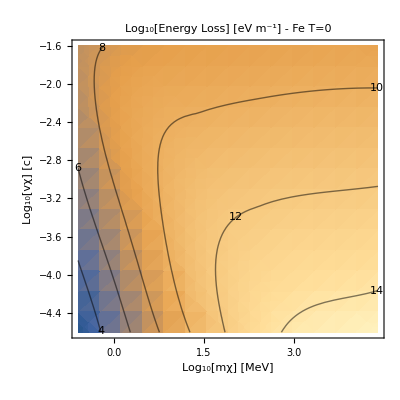

```mathematica
FeNuc0ELOutputDictSI  = EnergyLossTableAndInterNuc0[{2.5 10^5,2.5 10^10} ("JpereV")/("c")^2/.SIConstRepl,{2.5 10^-5,2.5 10^-2} "c" /.SIConstRepl,<|"mχ" -> 6, "vχ" -> 4|>,FeNucCoeffs,SIConstRepl,<|"nI"->nIFe|>,True,"FeNuc0ELOutputDict","Fe T=0",False];
PlotEL[FeNuc0ELOutputDictSI,"Fe T=0"]
```

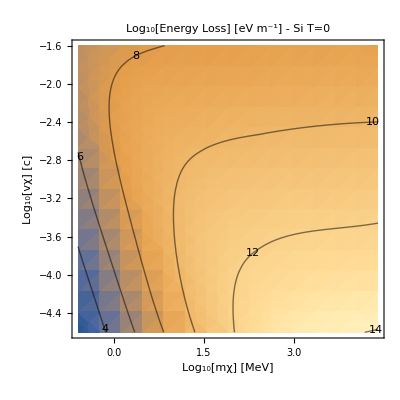

```mathematica
SiNuc0ELOutputDictSI  = EnergyLossTableAndInterNuc0[{2.5 10^5,2.5 10^10} ("JpereV")/("c")^2/.SIConstRepl,{2.5 10^-5,2.5 10^-2} "c" /.SIConstRepl,<|"mχ" -> 6, "vχ" -> 4|>,SiNucCoeffs,SIConstRepl,<|"nI"->nISi|>,True,"SiNuc0ELOutputDict","Si T=0",False];
PlotEL[SiNuc0ELOutputDictSI ,"Si T=0"]
```

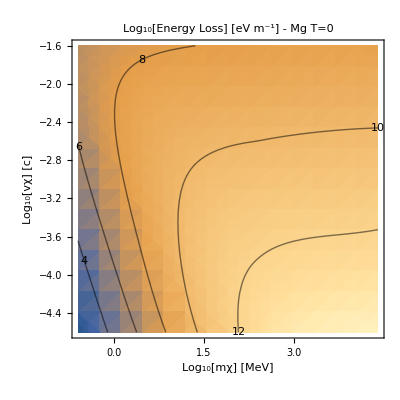

```mathematica
MgNuc0ELOutputDictSI  = EnergyLossTableAndInterNuc0[{2.5 10^5,2.5 10^10} ("JpereV")/("c")^2/.SIConstRepl,{2.5 10^-5,2.5 10^-2} "c" /.SIConstRepl,<|"mχ" -> 6, "vχ" -> 4|>,MgNucCoeffs,SIConstRepl,<|"nI"->nIMg|>,True,"MgNuc0ELOutputDict","Mg T=0",False];
PlotEL[MgNuc0ELOutputDictSI ,"Mg T=0"]
```

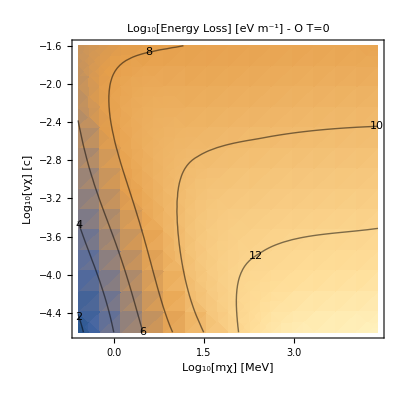

```mathematica
ONuc0ELOutputDictSI  = EnergyLossTableAndInterNuc0[{2.5 10^5,2.5 10^10} ("JpereV")/("c")^2/.SIConstRepl,{2.5 10^-5,2.5 10^-2} "c" /.SIConstRepl,<|"mχ" -> 6, "vχ" -> 4|>,ONucCoeffs,SIConstRepl,<|"nI"->nIO|>,True,"ONuc0ELOutputDict","O T=0",False];
PlotEL[ONuc0ELOutputDictSI ,"O T=0"]
```

#### Load EL dicts

```mathematica
FeNuc0ELOutputDictSI =ReadIt[NotebookDirectory[]<>"FeNuc0ELOutputDict"];
SiNuc0ELOutputDictSI =ReadIt[NotebookDirectory[]<>"SiNuc0ELOutputDict"];
{{MgNuc0ELOutputDictSI =ReadIt[NotebookDirectory[]<>"MgNuc0ELOutputDict"];}, {ONuc0ELOutputDictSI =ReadIt[NotebookDirectory[]<>"ONuc0ELOutputDict"];}}
```

{{Null},{Null}}

#### Function Modelling EL in the Earth

```mathematica
fEarth[mχ_,vχ_,r_]:= Module[{REarth = 6.371 10^6,rmantle =2.885 10^6,rcore},
rcore = REarth - rmantle;
Piecewise[{{FeNuc0ELOutputDictSI ["f"][mχ,vχ],Abs[r-REarth]<=rcore},{Log[10,0.447 10^SiNuc0ELOutputDictSI ["f"][mχ,vχ]+ 0.387 10^MgNuc0ELOutputDictSI["f"][mχ,vχ]+(2 0.447 + 0.387)10^ONuc0ELOutputDictSI["f"][mχ,vχ]],rcore<Abs[r-REarth]<REarth}},0]] (* see overleaf note on silicates, these are fractional abundances in the mantle - ignoring traces substances *)
```

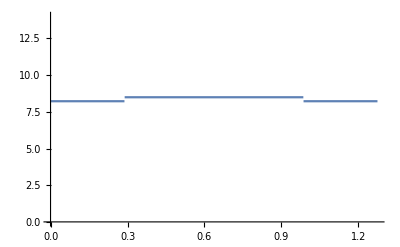

```mathematica
Plot[fEarth[Log[10,FeNuc0ELOutputDictSI[["kinlist"]][["mχ"]][[2]]],Log[10,FeNuc0ELOutputDictSI[["kinlist"]][["vχ"]][[2]]],r],{r,0,2Constants`REarth},PlotRange->{0,14}]
```

#### Compute κmin

InterpolatingFunction::dmval: Input value {-30.3516,11.4129} lies outside the range of data in the interpolating function. Extrapolation will be used.

General::stop: Further output of InterpolatingFunction::dmval will be suppressed during this calculation.

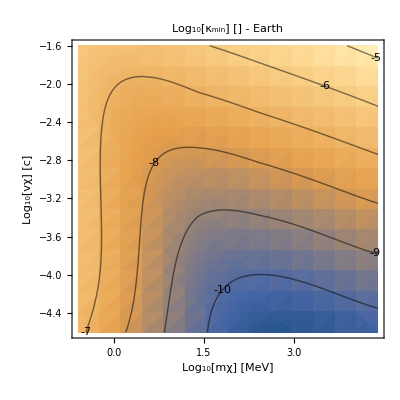

```mathematica
NκminT0 = κminInterpolationfnofr[FeNuc0ELOutputDictSI ,fEarth,0,(FeNuc0ELOutputDictSI [["f"]]@Domain),True];
```

#### minimum kinetic mixing comparison - Electron to Nuclear

```mathematica
eκminT0 = ReadIt[NotebookDirectory[]<>"../ELandKappamin/kappa min/eκminT0"];
```

```mathematica
Clear[interpolation]
title = "min(κ_N,κ_e)";
interpolation[mχ_,vχ_] := Min[eκminT0[["fκmin"]][mχ,vχ],NκminT0[["fκmin"]][mχ,vχ]];
kindict = eκminT0["ELdict"];
```

```mathematica
interpolation[-30,4]
```

-12.2799

******* SHOULD PUT THE Κ MIN PLOTTING INTO A MODULE

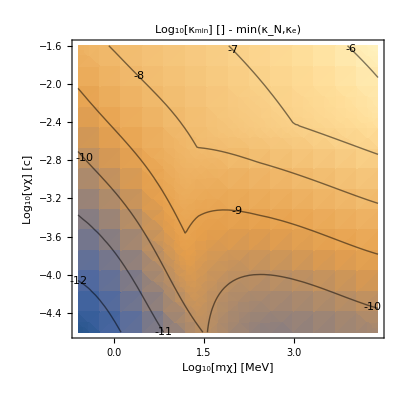

```mathematica
Show[{DensityPlot[interpolation[m+6-Log10[("c"^2)/("JpereV")/.Constants`SIConstRepl],v+Log10["c"/.Constants`SIConstRepl]],
	{m,Log[10,First[kindict[["kinlist"]][["mχ"]]]]-6+Log10[("c"^2)/("JpereV")/.Constants`SIConstRepl],Log[10,Last[kindict[["kinlist"]][["mχ"]]]]-6+Log10[("c"^2)/("JpereV")/.Constants`SIConstRepl]},
		{v,Log[10,First[kindict[["kinlist"]][["vχ"]]]]-Log10["c"/.Constants`SIConstRepl],Log[10,Last[kindict[["kinlist"]][["vχ"]]]]-Log10["c"/.Constants`SIConstRepl]},PlotRange->All,FrameLabel->{"\!\(\*SubscriptBox[\(Log\), \(10\)]\)[mχ] [MeV]","\!\(\*SubscriptBox[\(Log\), \(10\)]\)[vχ] [c]"},PlotLabel->StringForm["\!\(\*SubscriptBox[\(Log\), \(10\)]\)[\!\(\*SubscriptBox[\(κ\), \(min\)]\)] [] - ``",title]],
ContourPlot[interpolation[m+6- Log10[("c"^2)/("JpereV")/.Constants`SIConstRepl],v+Log10["c"/.Constants`SIConstRepl]],{m,Log[10,First[kindict[["kinlist"]][["mχ"]]]]-6+Log10[("c"^2)/("JpereV")/.Constants`SIConstRepl],Log[10,Last[kindict[["kinlist"]][["mχ"]]]]-6+Log10[("c"^2)/("JpereV")/.Constants`SIConstRepl]},
	{v,Log[10,First[kindict[["kinlist"]][["vχ"]]]]-Log10["c"/.Constants`SIConstRepl],Log[10,Last[kindict[["kinlist"]][["vχ"]]]]-Log10["c"/.Constants`SIConstRepl]},PlotRange->All,ContourLabels->True,ContourShading->False]}]
```

#### Energy Loss comparison - Iron

```mathematica
FeELOutputDict = ReadIt[NotebookDirectory[]<>"../ELandKappamin/compute energy loss/FeELOutputDictSI"];
```

```mathematica
Clear[FeENucDiff]
FeENucDiff[mχ_,vχ_]:=FeELOutputDict[["f"]][mχ,vχ]-FeNuc0ELOutputDictSI[["f"]][mχ,vχ]
```

```mathematica
FeENucDiff[-28,4]
```

-1.57991

```mathematica
ELDictDiff = <|"f"->FeENucDiff,"kinlist"->kindict[["kinlist"]]|>;
```

```mathematica
kindict[["kinlist"]]
```

<|mχ→{4.45×10^-31,4.45×10^-30,4.45×10^-29,4.45×10^-28,4.45×10^-27,4.45×10^-26},vχ→{7500.,75000.,750000.,7.5×10^6}|>

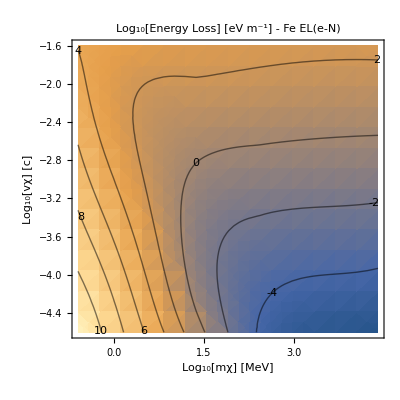

```mathematica
PlotEL[ELDictDiff,"Fe EL(e-N)"]
```

### Finite Temperature

#### Find Number Density of each material

```mathematica
nIFe = nIFromDensity[13000,FeNucCoeffs[["mN"]]] (* [m^-3] iron at core*) 
nISi = nIFromDensity[2330,SiNucCoeffs[["mN"]]](* [m^-3] Si at crust*) 
nIMg = nIFromDensity[1738,MgNucCoeffs[["mN"]]](* [m^-3] Mg at crust*) 
nIO = nIFromDensity[1738,ONucCoeffs[["mN"]]](* [m^-3] O at crust*)
```

1.39845×10^29

5.01291×10^28

4.36245×10^28

6.54367×10^28

#### Compute Energy Loss and Interpolation

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in EnergyLoss`Private`q near {EnergyLoss`Private`q} = {5.25128×10^7}. NIntegrate obtained 9.81961×10^-46 and 8.48609×10^-49 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in EnergyLoss`Private`q near {EnergyLoss`Private`q} = {2.75089×10^8}. NIntegrate obtained 1.68705×10^-44 and 8.66989×10^-46 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in EnergyLoss`Private`q near {EnergyLoss`Private`q} = {1.01804×10^9}. NIntegrate obtained 3.69718×10^-43 and 7.47706×10^-44 for the integral and error estimates.

General::stop: Further output of NIntegrate::ncvb will be suppressed during this calculation.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

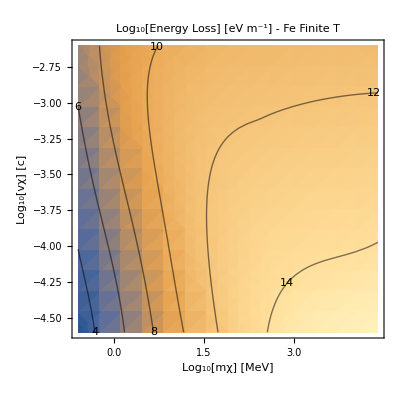

```mathematica
FeNuc0ELOutputDictSI  = EnergyLossTableAndInterNuc[{2.5 10^5,2.5 10^10} ("JpereV")/("c")^2/.SIConstRepl,{2.5 10^-5,2.5 10^-3} "c" /.SIConstRepl,<|"mχ" -> 6, "vχ" -> 4|>,FeNucCoeffs,SIConstRepl,<|"nI"->nIFe,"β"->βcore|>,True,"FeNucELOutputDict","Fe Finite T",False];
PlotEL[FeNuc0ELOutputDictSI,"Fe Finite T"]
```

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in EnergyLoss`Private`q near {EnergyLoss`Private`q} = {5.25128×10^7}. NIntegrate obtained 1.10009×10^-45 and 3.06675×10^-47 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in EnergyLoss`Private`q near {EnergyLoss`Private`q} = {2.75089×10^8}. NIntegrate obtained 2.374×10^-44 and 6.02188×10^-46 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in EnergyLoss`Private`q near {EnergyLoss`Private`q} = {1.01804×10^9}. NIntegrate obtained 5.10891×10^-43 and 1.03301×10^-43 for the integral and error estimates.

General::stop: Further output of NIntegrate::ncvb will be suppressed during this calculation.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

General::stop: Further output of NIntegrate::slwcon will be suppressed during this calculation.

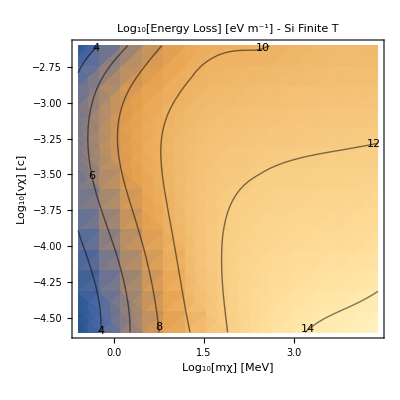

```mathematica
SiNucELOutputDictSI  = EnergyLossTableAndInterNuc[{2.5 10^5,2.5 10^10} ("JpereV")/("c")^2/.SIConstRepl,{2.5 10^-5,2.5 10^-3} "c" /.SIConstRepl,<|"mχ" -> 6, "vχ" -> 4|>,SiNucCoeffs,SIConstRepl,<|"nI"->nISi,"β"->βcrust|>,True,"SiNucELOutputDict","Si Finite T",False];
PlotEL[SiNucELOutputDictSI ,"Si Finite T"]
```

```mathematica
EnergyLossTableAndInterNuc[{2.5 10^5,2.5 10^10} ("JpereV")/("c")^2/.SIConstRepl,{2.5 10^-5,2.5 10^-3} "c" /.SIConstRepl,<|"mχ" -> 6, "vχ" -> 4|>,SiNucCoeffs,SIConstRepl,<|"nI"->nISi,"β"->βcrust|>,False,"SiNucELOutputDict","Si Finite T",False];
```

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in EnergyLoss`Private`q near {EnergyLoss`Private`q} = {5.25128×10^7}. NIntegrate obtained 1.10009×10^-45 and 3.06675×10^-47 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in EnergyLoss`Private`q near {EnergyLoss`Private`q} = {2.75089×10^8}. NIntegrate obtained 2.374×10^-44 and 6.02188×10^-46 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in EnergyLoss`Private`q near {EnergyLoss`Private`q} = {1.01804×10^9}. NIntegrate obtained 5.10891×10^-43 and 1.03301×10^-43 for the integral and error estimates.

General::stop: Further output of NIntegrate::ncvb will be suppressed during this calculation.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

General::stop: Further output of NIntegrate::slwcon will be suppressed during this calculation.

```mathematica
MgNucELOutputDictSI  = EnergyLossTableAndInterNuc[{2.5 10^5,2.5 10^10} ("JpereV")/("c")^2/.SIConstRepl,{2.5 10^-5,2.5 10^-3} "c" /.SIConstRepl,<|"mχ" -> 6, "vχ" -> 4|>,MgNucCoeffs,SIConstRepl,<|"nI"->nIMg,"β"->βcrust|>,True,"MgNucELOutputDict","Mg Finite T",True];
PlotEL[MgNucELOutputDictSI ,"Mg Finite T"]
```

NIntegrate::izero: Integral and error estimates are 0 on all integration subregions. Try increasing the value of the MinRecursion option. If value of integral may be 0, specify a finite value for the AccuracyGoal option.

For mχ = 4.45×10^-31 , vχ = 7500.
dEdr:	0.

NIntegrate::izero: Integral and error estimates are 0 on all integration subregions. Try increasing the value of the MinRecursion option. If value of integral may be 0, specify a finite value for the AccuracyGoal option.

For mχ = 4.45×10^-31 , vχ = 34811.9
dEdr:	0.

NIntegrate::izero: Integral and error estimates are 0 on all integration subregions. Try increasing the value of the MinRecursion option. If value of integral may be 0, specify a finite value for the AccuracyGoal option.

General::stop: Further output of NIntegrate::izero will be suppressed during this calculation.

For mχ = 4.45×10^-31 , vχ = 161583.
dEdr:	0.

For mχ = 4.45×10^-31 , vχ = 750000.
dEdr:	0.

For mχ = 4.45×10^-30 , vχ = 7500.
dEdr:	0.

For mχ = 4.45×10^-30 , vχ = 34811.9
dEdr:	0.

For mχ = 4.45×10^-30 , vχ = 161583.
dEdr:	0.

For mχ = 4.45×10^-30 , vχ = 750000.
dEdr:	0.

For mχ = 4.45×10^-29 , vχ = 7500.
dEdr:	0.

For mχ = 4.45×10^-29 , vχ = 34811.9
dEdr:	0.

For mχ = 4.45×10^-29 , vχ = 161583.
dEdr:	0.

For mχ = 4.45×10^-29 , vχ = 750000.
dEdr:	0.

For mχ = 4.45×10^-28 , vχ = 7500.
dEdr:	0.

For mχ = 4.45×10^-28 , vχ = 34811.9
dEdr:	0.

For mχ = 4.45×10^-28 , vχ = 161583.
dEdr:	0.

For mχ = 4.45×10^-28 , vχ = 750000.
dEdr:	0.

For mχ = 4.45×10^-27 , vχ = 7500.
dEdr:	0.

For mχ = 4.45×10^-27 , vχ = 34811.9
dEdr:	0.

For mχ = 4.45×10^-27 , vχ = 161583.
dEdr:	0.

For mχ = 4.45×10^-27 , vχ = 750000.
dEdr:	0.

For mχ = 4.45×10^-26 , vχ = 7500.
dEdr:	0.

For mχ = 4.45×10^-26 , vχ = 34811.9
dEdr:	0.

For mχ = 4.45×10^-26 , vχ = 161583.
dEdr:	0.

For mχ = 4.45×10^-26 , vχ = 750000.
dEdr:	0.

-Graphics-

```mathematica
ONucELOutputDictSI  = EnergyLossTableAndInterNuc0[{2.5 10^5,2.5 10^10} ("JpereV")/("c")^2/.SIConstRepl,{2.5 10^-5,2.5 10^-2} "c" /.SIConstRepl,<|"mχ" -> 6, "vχ" -> 4|>,ONucCoeffs,SIConstRepl,<|"nI"->nIO|>,True,"ONucELOutputDict","O Finite T",False];
PlotEL[ONucELOutputDictSI ,"O Finite T"]
```

-Graphics-

#### Load EL dicts

```mathematica
FeNuc0ELOutputDictSI =ReadIt[NotebookDirectory[]<>"FeNuc0ELOutputDict"];
SiNuc0ELOutputDictSI =ReadIt[NotebookDirectory[]<>"SiNuc0ELOutputDict"];
{{MgNuc0ELOutputDictSI =ReadIt[NotebookDirectory[]<>"MgNuc0ELOutputDict"];}, {ONuc0ELOutputDictSI =ReadIt[NotebookDirectory[]<>"ONuc0ELOutputDict"];}}
```

{{Null},{Null}}

#### Function Modelling EL in the Earth

```mathematica
fEarth[mχ_,vχ_,r_]:= Module[{REarth = 6.371 10^6,rmantle =2.885 10^6,rcore},
rcore = REarth - rmantle;
Piecewise[{{FeNuc0ELOutputDictSI ["f"][mχ,vχ],Abs[r-REarth]<=rcore},{Log[10,0.447 10^SiNuc0ELOutputDictSI ["f"][mχ,vχ]+ 0.387 10^MgNuc0ELOutputDictSI["f"][mχ,vχ]+(2 0.447 + 0.387)10^ONuc0ELOutputDictSI["f"][mχ,vχ]],rcore<Abs[r-REarth]<REarth}},0]] (* see overleaf note on silicates, these are fractional abundances in the mantle - ignoring traces substances *)
```

```mathematica
Plot[fEarth[Log[10,FeNuc0ELOutputDictSI[["kinlist"]][["mχ"]][[2]]],Log[10,FeNuc0ELOutputDictSI[["kinlist"]][["vχ"]][[2]]],r],{r,0,2Constants`REarth},PlotRange->{0,14}]
```

-Graphics-

#### Compute κmin

```mathematica
κminInterpolationfnofr[FeNuc0ELOutputDictSI ,fEarth,0,(FeNuc0ELOutputDictSI [["f"]]@Domain),True]
```

InterpolatingFunction::dmval: Input value {-30.3516,11.4129} lies outside the range of data in the interpolating function. Extrapolation will be used.

General::stop: Further output of InterpolatingFunction::dmval will be suppressed during this calculation.

-Graphics-

<|table→{{1.51396×10^-7,4.79004×10^-9,1.5793×10^-10,1.68131×10^-11,1.71632×10^-11,3.84656×10^-11},{3.7273×10^-7,1.1173×10^-8,5.8693×10^-10,4.11688×10^-10,8.37885×10^-10,2.17454×10^-9},{4.91219×10^-7,2.11705×10^-8,1.28159×10^-8,2.60552×10^-8,6.61967×10^-8,1.86765×10^-7},{6.68399×10^-7,3.75916×10^-7,8.44109×10^-7,2.1126×10^-6,5.851×10^-6,0.0000181734}},fκmin→InterpolatingFunction[…],ELdict→<|f→InterpolatingFunction[…],mχMesh→{{4.45×10^-31,4.45×10^-31,4.45×10^-31,4.45×10^-31},{4.45×10^-30,4.45×10^-30,4.45×10^-30,4.45×10^-30},{4.45×10^-29,4.45×10^-29,4.45×10^-29,4.45×10^-29},{4.45×10^-28,4.45×10^-28,4.45×10^-28,4.45×10^-28},{4.45×10^-27,4.45×10^-27,4.45×10^-27,4.45×10^-27},{4.45×10^-26,4.45×10^-26,4.45×10^-26,4.45×10^-26}},vχMesh→{{7500.,75000.,750000.,7.5×10^6},{7500.,75000.,750000.,7.5×10^6},{7500.,75000.,750000.,7.5×10^6},{7500.,75000.,750000.,7.5×10^6},{7500.,75000.,750000.,7.5×10^6},{7500.,75000.,750000.,7.5×10^6}},EnergyLossMesh→{{339.298,33900.9,3.12074×10^6,2.78265×10^7},{3.38951×10^6,3.12022×10^8,2.78242×10^9,2.95747×10^8},{3.11507×10^10,2.78012×10^11,2.95679×10^10,6.56856×10^8},{2.75727×10^13,2.95005×10^12,6.56182×10^10,1.01567×10^9},{2.88422×10^14,6.49598×10^12,1.00923×10^11,1.26429×10^9},{5.9558×10^14,9.55987×10^12,1.25316×10^11,1.26622×10^9}},params→{e→1.60289×10^-19,m→9.11×10^-31,hbar→1.055×10^-34,ℏ→1.055×10^-34,c→300000000,α→1/137,ϵ0→8.85×10^-12,JpereV→1.602×10^-19,kB→1.381×10^-23},fname→FeNuc0ELOutputDict,kinlist→<|mχ→{4.45×10^-31,4.45×10^-30,4.45×10^-29,4.45×10^-28,4.45×10^-27,4.45×10^-26},vχ→{7500.,75000.,750000.,7.5×10^6}|>,meshdims→<|mχ→6,vχ→4|>,ϵ→O T=0|>,fEL→fEarth,vescape→0|>

### Original - wider mass range

#### Compute Energy Loss and Interpolation

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in EnergyLoss`Private`q near {EnergyLoss`Private`q} = {4.69826×10^10}. NIntegrate obtained 5.12656×10^-25 and 1.81427×10^-30 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in EnergyLoss`Private`q near {EnergyLoss`Private`q} = {3.46268×10^10}. NIntegrate obtained 5.12656×10^-25 and 6.59331×10^-30 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in EnergyLoss`Private`q near {EnergyLoss`Private`q} = {1.86298×10^11}. NIntegrate obtained 5.12656×10^-25 and 4.9281×10^-30 for the integral and error estimates.

General::stop: Further output of NIntegrate::ncvb will be suppressed during this calculation.

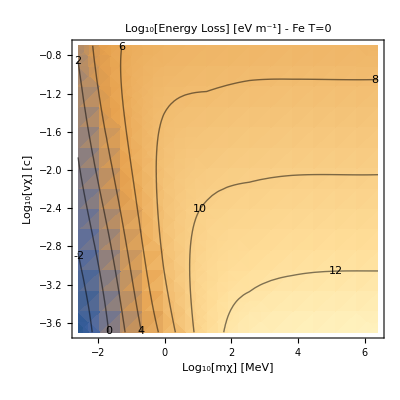

```mathematica
FeNuc0ELOutputDictSI  = EnergyLossTableAndInterNuc0[{2.5 10^3,2.5 10^12} ("JpereV")/("c")^2/.SIConstRepl,{2 10^-4,2 10^-1} "c" /.SIConstRepl,<|"mχ" -> 8, "vχ" -> 4|>,FeNucCoeffs,SIConstRepl,<|"nI"->nIFe|>,True,"FeNuc0ELOutputDict","Fe T=0",False];
PlotEL[FeNuc0ELOutputDictSI,"Fe T=0"]
```

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in EnergyLoss`Private`q near {EnergyLoss`Private`q} = {1.94331×10^11}. NIntegrate obtained 2.88794×10^-25 and 8.3854×10^-31 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in EnergyLoss`Private`q near {EnergyLoss`Private`q} = {7.91364×10^10}. NIntegrate obtained 2.88794×10^-25 and 3.56008×10^-31 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in EnergyLoss`Private`q near {EnergyLoss`Private`q} = {1.71776×10^11}. NIntegrate obtained 2.88794×10^-25 and 1.86679×10^-30 for the integral and error estimates.

General::stop: Further output of NIntegrate::ncvb will be suppressed during this calculation.

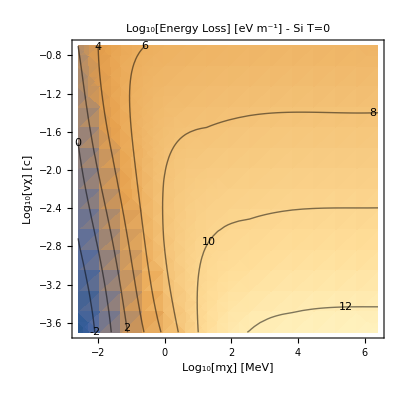

```mathematica
SiNuc0ELOutputDictSI  = EnergyLossTableAndInterNuc0[{2.5 10^3,2.5 10^12} ("JpereV")/("c")^2/.SIConstRepl,{2 10^-4,2 10^-1} "c" /.SIConstRepl,<|"mχ" -> 8, "vχ" -> 4|>,SiNucCoeffs,SIConstRepl,<|"nI"->nISi|>,True,"SiNuc0ELOutputDict","Si T=0",False];
PlotEL[SiNuc0ELOutputDictSI ,"Si T=0"]
```

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in EnergyLoss`Private`q near {EnergyLoss`Private`q} = {4.07927×10^10}. NIntegrate obtained 2.53333×10^-25 and 1.23286×10^-30 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in EnergyLoss`Private`q near {EnergyLoss`Private`q} = {6.94974×10^10}. NIntegrate obtained 2.53333×10^-25 and 3.24375×10^-31 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in EnergyLoss`Private`q near {EnergyLoss`Private`q} = {1.50853×10^11}. NIntegrate obtained 2.53333×10^-25 and 1.60984×10^-30 for the integral and error estimates.

General::stop: Further output of NIntegrate::ncvb will be suppressed during this calculation.

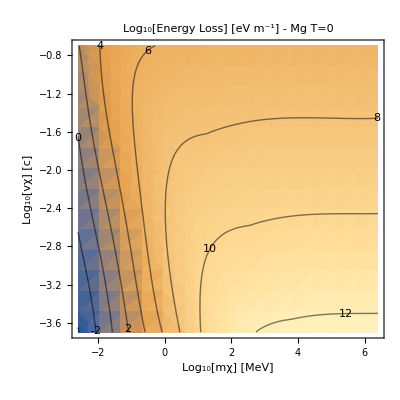

```mathematica
MgNuc0ELOutputDictSI  = EnergyLossTableAndInterNuc0[{2.5 10^3,2.5 10^12} ("JpereV")/("c")^2/.SIConstRepl,{2 10^-4,2 10^-1} "c" /.SIConstRepl,<|"mχ" -> 8, "vχ" -> 4|>,MgNucCoeffs,SIConstRepl,<|"nI"->nIMg|>,True,"MgNuc0ELOutputDict","Mg T=0",False];
PlotEL[MgNuc0ELOutputDictSI ,"Mg T=0"]
```

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in EnergyLoss`Private`q near {EnergyLoss`Private`q} = {1.68505×10^11}. NIntegrate obtained 1.8712×10^-25 and 6.00533×10^-31 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in EnergyLoss`Private`q near {EnergyLoss`Private`q} = {1.05764×10^11}. NIntegrate obtained 1.8712×10^-25 and 1.95241×10^-30 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in EnergyLoss`Private`q near {EnergyLoss`Private`q} = {1.17252×10^11}. NIntegrate obtained 1.8712×10^-25 and 1.0155×10^-30 for the integral and error estimates.

General::stop: Further output of NIntegrate::ncvb will be suppressed during this calculation.

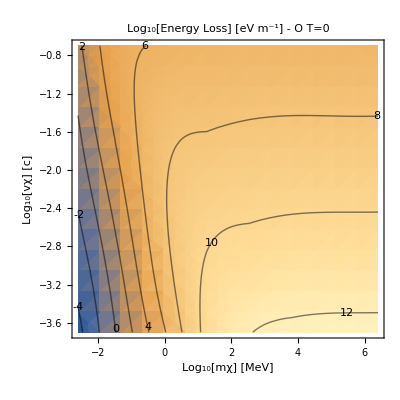

```mathematica
ONuc0ELOutputDictSI  = EnergyLossTableAndInterNuc0[{2.5 10^3,2.5 10^12} ("JpereV")/("c")^2/.SIConstRepl,{2 10^-4,2 10^-1} "c" /.SIConstRepl,<|"mχ" -> 8, "vχ" -> 4|>,ONucCoeffs,SIConstRepl,<|"nI"->nIO|>,True,"ONuc0ELOutputDict","O T=0",False];
PlotEL[ONuc0ELOutputDictSI ,"O T=0"]
```

#### figure out scalings and cutoff

```mathematica
{2.5 10^3,2.5 10^12} ("JpereV")/("c")^2/.SIConstRepl
```

{4.45×10^-33,4.45×10^-24}

```mathematica
100 keV/c >= √(mN mχ) vχ
```

upper bound in q is:

```mathematica
√(2 mN Eχ 4  μ^2/(mχ mN))== √(v^2 4  μ^2)<= 100 keV / c
```

for mχ << mN, μ ~ mχ, so we have the condition

```mathematica
v 2  mχ<= 100 keV / c 
mχ<= 1/(2 v)100 keV / c
```

#### Load EL dicts

```mathematica
FeNuc0ELOutputDictSI =ReadIt[NotebookDirectory[]<>"FeNuc0ELOutputDict"];
SiNuc0ELOutputDictSI =ReadIt[NotebookDirectory[]<>"SiNuc0ELOutputDict"];
{{MgNuc0ELOutputDictSI =ReadIt[NotebookDirectory[]<>"MgNuc0ELOutputDict"];}, {ONuc0ELOutputDictSI =ReadIt[NotebookDirectory[]<>"ONuc0ELOutputDict"];}}
```

{{Null},{Null}}

#### Function Modelling EL in the Earth

```mathematica
fEarth[mχ_,vχ_,r_]:= Module[{REarth = 6.371 10^6,rmantle =2.885 10^6,rcore},
rcore = REarth - rmantle;
Piecewise[{{FeNuc0ELOutputDictSI ["f"][mχ,vχ],Abs[r-REarth]<=rcore},{Log[10,0.447 10^SiNuc0ELOutputDictSI ["f"][mχ,vχ]+ 0.387 10^MgNuc0ELOutputDictSI["f"][mχ,vχ]+(2 0.447 + 0.387)10^ONuc0ELOutputDictSI["f"][mχ,vχ]],rcore<Abs[r-REarth]<REarth}},0]] (* see overleaf note on silicates, these are fractional abundances in the mantle - ignoring traces substances *)
```

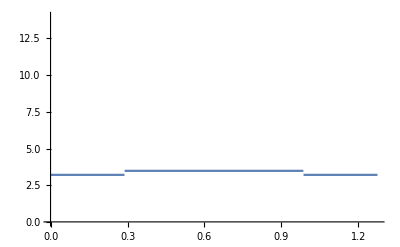

```mathematica
Plot[fEarth[Log[10,FeNuc0ELOutputDictSI[["kinlist"]][["mχ"]][[2]]],Log[10,FeNuc0ELOutputDictSI[["kinlist"]][["vχ"]][[2]]],r],{r,0,2Constants`REarth},PlotRange->{0,14}]
```

#### Compute κmin

InterpolatingFunction::dmval: Input value {-32.3516,12.4129} lies outside the range of data in the interpolating function. Extrapolation will be used.

General::stop: Further output of InterpolatingFunction::dmval will be suppressed during this calculation.

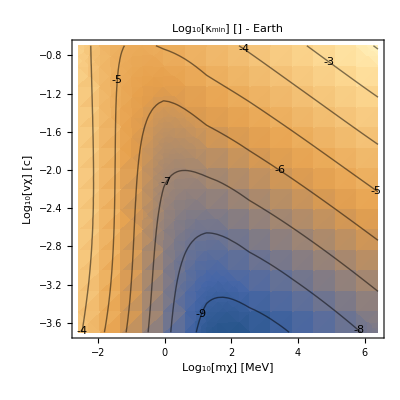

```mathematica
NκminT0 = κminInterpolationfnofr[FeNuc0ELOutputDictSI ,fEarth,vescape,(FeNuc0ELOutputDictSI [["f"]]@Domain),True];
```

#### minimum kinetic mixing comparison - Electron to Nuclear

```mathematica
eκminT0 = ReadIt[NotebookDirectory[]<>"../ELandKappamin/kappa min/eκminenhanced"];
```

```mathematica
Clear[interpolation]
title = "min(κ_N,κ_e)";
interpolation[mχ_,vχ_] := Min[eκminT0[["fκmin"]][mχ,vχ],NκminT0[["fκmin"]][mχ,vχ]];
kindict = eκminT0["ELdict"];
```

```mathematica
interpolation[-30,4]
```

-12.2799

******* SHOULD PUT THE Κ MIN PLOTTING INTO A MODULE

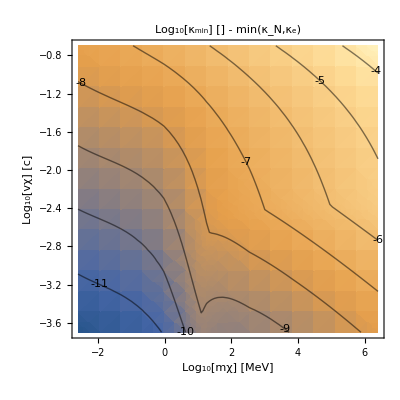

```mathematica
Show[{DensityPlot[interpolation[m+6-Log10[("c"^2)/("JpereV")/.Constants`SIConstRepl],v+Log10["c"/.Constants`SIConstRepl]],
	{m,Log[10,First[kindict[["kinlist"]][["mχ"]]]]-6+Log10[("c"^2)/("JpereV")/.Constants`SIConstRepl],Log[10,Last[kindict[["kinlist"]][["mχ"]]]]-6+Log10[("c"^2)/("JpereV")/.Constants`SIConstRepl]},
		{v,Log[10,First[kindict[["kinlist"]][["vχ"]]]]-Log10["c"/.Constants`SIConstRepl],Log[10,Last[kindict[["kinlist"]][["vχ"]]]]-Log10["c"/.Constants`SIConstRepl]},PlotRange->All,FrameLabel->{"\!\(\*SubscriptBox[\(Log\), \(10\)]\)[mχ] [MeV]","\!\(\*SubscriptBox[\(Log\), \(10\)]\)[vχ] [c]"},PlotLabel->StringForm["\!\(\*SubscriptBox[\(Log\), \(10\)]\)[\!\(\*SubscriptBox[\(κ\), \(min\)]\)] [] - ``",title]],
ContourPlot[interpolation[m+6- Log10[("c"^2)/("JpereV")/.Constants`SIConstRepl],v+Log10["c"/.Constants`SIConstRepl]],{m,Log[10,First[kindict[["kinlist"]][["mχ"]]]]-6+Log10[("c"^2)/("JpereV")/.Constants`SIConstRepl],Log[10,Last[kindict[["kinlist"]][["mχ"]]]]-6+Log10[("c"^2)/("JpereV")/.Constants`SIConstRepl]},
	{v,Log[10,First[kindict[["kinlist"]][["vχ"]]]]-Log10["c"/.Constants`SIConstRepl],Log[10,Last[kindict[["kinlist"]][["vχ"]]]]-Log10["c"/.Constants`SIConstRepl]},PlotRange->All,ContourLabels->True,ContourShading->False]}]
```

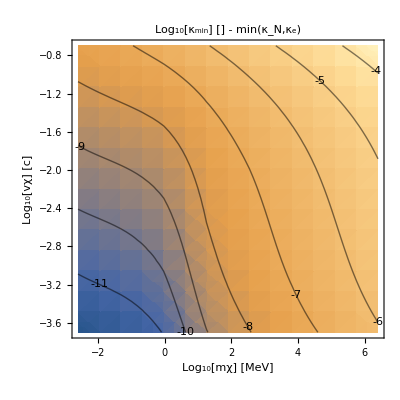

```mathematica
Show[{DensityPlot[interpolation[m+6-Log10[("c"^2)/("JpereV")/.Constants`SIConstRepl],v+Log10["c"/.Constants`SIConstRepl]],
	{m,Log[10,First[kindict[["kinlist"]][["mχ"]]]]-6+Log10[("c"^2)/("JpereV")/.Constants`SIConstRepl],Log[10,Last[kindict[["kinlist"]][["mχ"]]]]-6+Log10[("c"^2)/("JpereV")/.Constants`SIConstRepl]},
		{v,Log[10,First[kindict[["kinlist"]][["vχ"]]]]-Log10["c"/.Constants`SIConstRepl],Log[10,Last[kindict[["kinlist"]][["vχ"]]]]-Log10["c"/.Constants`SIConstRepl]},PlotRange->All,FrameLabel->{"\!\(\*SubscriptBox[\(Log\), \(10\)]\)[mχ] [MeV]","\!\(\*SubscriptBox[\(Log\), \(10\)]\)[vχ] [c]"},PlotLabel->StringForm["\!\(\*SubscriptBox[\(Log\), \(10\)]\)[\!\(\*SubscriptBox[\(κ\), \(min\)]\)] [] - ``",title]],
ContourPlot[interpolation[m+6- Log10[("c"^2)/("JpereV")/.Constants`SIConstRepl],v+Log10["c"/.Constants`SIConstRepl]],{m,Log[10,First[kindict[["kinlist"]][["mχ"]]]]-6+Log10[("c"^2)/("JpereV")/.Constants`SIConstRepl],Log[10,Last[kindict[["kinlist"]][["mχ"]]]]-6+Log10[("c"^2)/("JpereV")/.Constants`SIConstRepl]},
	{v,Log[10,First[kindict[["kinlist"]][["vχ"]]]]-Log10["c"/.Constants`SIConstRepl],Log[10,Last[kindict[["kinlist"]][["vχ"]]]]-Log10["c"/.Constants`SIConstRepl]},PlotRange->All,ContourLabels->True,ContourShading->False]}]
```

#### Energy Loss comparison - Iron

```mathematica
FeELOutputDict = ReadIt[NotebookDirectory[]<>"../ELandKappamin/compute energy loss/FeELOutputDictSIEnhanced"];
```

```mathematica
Clear[FeENucDiff]
FeENucDiff[mχ_,vχ_]:=FeELOutputDict[["f"]][mχ,vχ]-FeNuc0ELOutputDictSI[["f"]][mχ,vχ]
```

```mathematica
ELDictDiff = <|"f"->FeENucDiff,"kinlist"->kindict[["kinlist"]]|>;
```

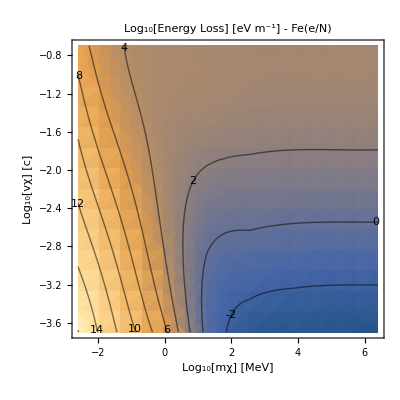

```mathematica
PlotEL[ELDictDiff,"Fe(e/N)"]
```